## CS 533 Image Processing End-of-Semester Project: Chernoff Faces & Photos Note: Please evaluate the functions chernoffFace[], chernoffFaceAnimateWithWeatherData[] and chernoffFaceAnimateWithCountryLatitudeData[] before checking outputs.

### Chernoff Faces

A Chernoff face is a simple sketch of a human face that is parameterized by a few variables. By manipulating the variables, it is possible to achieve a wide range of expressions. Here are a few auxiliary functions (evaluate these before running the Manipulate) below.

```mathematica
face=Circle[{0,0},{1,1.2}];pupNow={0,0};left=1;right=2;
eyeRadius=0.18;eyeCenter={{-0.4,0.15},{0.4,0.15}};pupilRadius=0.09;
browUp=0.25;browW=0.2;browAng=Pi/20;
eye[side_,eccen_]:={Black,Circle[eyeCenter[[side]],{eyeRadius+0.05,eyeRadius+eccen}]};
pupil[side_,pup_,eccen_]:={Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},pupilRadius+Max[0,eccen/3]],Black,Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},0.03]};
browDraw[side_,{browAng_,browLift_},eccen_]:=Rotate[{Thickness[0.01],Line[{{eyeCenter[[side]]+{-browW,browLift+browUp+0.5 eccen},eyeCenter[[side]]+{browW,browLift+browUp+0.5 eccen}}}]},2 (side-1.5) browAng];
mouthDraw[s_]:=ParametricPlot[{Cos[u],-s Sin[u]},{u,Pi/6,Pi-Pi/6},Axes->False,PlotStyle->{Red,Thickness[0.02]},PlotRange->All];
```

Now you can create many expressive faces by moving the sliders and grabbing the eyes with the mouse. See if you can make it happy. Sad? Angry?

```mathematica
Manipulate[eyeMat={{1/(eyeRadius-pupilRadius/2),0},{0,1/(0.15+eyes-pupilRadius/2)}};
If[Norm[eyeMat.(pup-eyeCenter[[left]])]<1,pupNow=pup-eyeCenter[[left]];];
If[Norm[eyeMat.(pup-eyeCenter[[right]])]<1,pupNow=pup-eyeCenter[[right]];];
Graphics[{face,eye[left,eyes],eye[right,eyes],Blue,pupil[left,pupNow,eyes],pupil[right,pupNow,eyes],Black,browDraw[left,brows,eyes],browDraw[right,brows,eyes],Inset[mouthDraw[mouth],{0,-0.5}]},ImageSize->{400,450}],{{brows,{-Pi/20,0}},{-0.6,0},{0.6,0.15},ControlPlacement->Left},{{eyes,0},-0.07,0.07,ControlPlacement->Left,ControlType->VerticalSlider},{{mouth,0.15},-0.401,0.4,0.01,ControlPlacement->Left,ControlType->VerticalSlider},{{pup,{0,0}},Locator,Appearance->None},SaveDefinitions->True]
```

I originally wrote this in answer to a StackExchange question:

```mathematica
URL["https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face"]
```

URL[https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face]

### Chernoff Photos #1

Your goal in this part of the project is to start with a full-face photo, and to create a Manipulate that will cause the photo to undergo expression changes analogous to the simple line drawing above. So if your friend in the photo is smiling, you can grab the mouth slider and make them sad. If their eyebrows are curved gently down, you can make them angry by moving the brows slider. If the eyes are narrow, you can widen them with the eye slider to make them look surprised.

In order to accomplish this task, you will need to locate facial features. Fortunately, there is a command called

```mathematica
?FacialFeatures
```

that does a pretty reasonable job. You will want to study the help file for this function. The parent function FeatureExtract may also be useful (though it may not be needed, depending on how you proceed). Of course, you will also want to use some of the spatial mapping functions like those in the Spatial Mappings section of the Visual Vocabulary.

Start with some of the photos from actors and characters from Game of Thrones. Then do the same kind of thing for (at least) 3 other photo images of faces. Perhaps a self-portrait would be fitting.

For this project, you should pass in your function (a Manipulate somewhat similar to the above) along with several examples of how it works on photos of different faces. Show that you can make the faces change expressions. Good luck and have fun!

```mathematica
gamePeople=-Graphics-;
```

By googling around, you can find an alternative implementation of Chernoff faces:

```mathematica
URL["https://mathematicaforprediction.wordpress.com/2016/06/03/making-chernoff-faces-for-data-visualization/"]
```

URL[https://mathematicaforprediction.wordpress.com/2016/06/03/making-chernoff-faces-for-data-visualization/]

This link also has a nice writeup about how to use Chernoff faces for data visualization. Feel free to use this or other accessible resources if they are helpful.

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
person1=Import["person1.jpg"];
person2 = Import["person2.jpg"];
person3=Import["person3.jpg"];
person4 = Import["person4.jpg"];
daenerys = Import["daenerys.jpg"];
jon = Import["jon.jpg"];
khal = Import["khal.jpg"];
sansa = Import["sansa.png"];
GraphicsRow[{person1,person2,person3,person4},ImageSize->Large]
```

-Graphics-

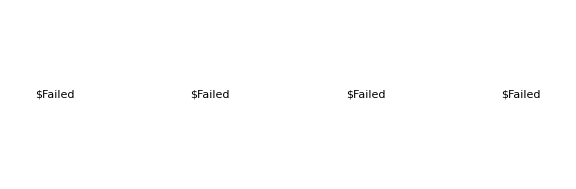

```mathematica
GraphicsRow[{daenerys,jon,khal,sansa},ImageSize->Large]
```

-Graphics-

```mathematica
chernoffFace[image_]:= Module[{},

(*Function to change eye features in a face*)
(*This function enlarges/diminishes eye by calculating the mean position of all eye points 
and then using the slope of each eye point from the mean position to get the direction in which to
enlarge/diminish the eye. Here the diff variable captures the slope(direction of change for x and y coordinates).*)
manipulateEyes[grid_,leftEyeIndex_,rightEyeIndex_,scale_]:=Module[{},tempGrid=grid;
leftEyeCenter=Mean[tempGrid[[leftEyeIndex]]];
For[i=1,i≤Length[leftEyeIndex],i++,diff=tempGrid[[leftEyeIndex[[i]]]]-leftEyeCenter;
tempGrid[[leftEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[leftEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

rightEyeCenter=Mean[tempGrid[[rightEyeIndex]]];
For[i=1,i≤Length[rightEyeIndex],i++,diff=tempGrid[[rightEyeIndex[[i]]]]-rightEyeCenter;
tempGrid[[rightEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[rightEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

tempGrid];

(*Function to change mouth features in a face*)
(*This function alters the smile points by first calculating the mean position of all mouth points
and then based on the square of the distance from the mean position, the y-coordinate of all
mouth positions are increased/decreased to create smile/frown.*)
manipulateMouth[grid_,mouthIndex_,scale_]:=Module[{},tempGrid=grid;
For[i=1,i≤Length[mouthIndex],i++,
tempGrid[[mouthIndex[[i]]]][[2]]+=scale*(tempGrid[[mouthIndex[[i]]]][[1]]-Mean[tempGrid[[mouthIndex]]][[1]])^2;];
tempGrid];

(*Function to change eyebrow features in a face*)
(*This function alters the eyebrow points by first calculating mean position for both left and right eyebrow points.
Then based on scale value, it increases/decreases the y coordinates of eyebrow points based on whether an
eyebrow point is left/right of the mean position for each eyebrow. Amount of change is relative to difference
between x-coordinates of mean eyebrow point and the eyebrow point. *)
manipulateEyeBrows[grid_,leftEyeBrowIndex_,rightEyeBrowIndex_,scale_]:=Module[{},tempGrid=grid;
temp=scale;
For[i=1,i≤Length[leftEyeBrowIndex],i++,If[i≤Length[leftEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[leftEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[leftEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[leftEyeBrowIndex]]][[1]]);];
temp=scale;
For[i=1,i≤Length[rightEyeBrowIndex],i++,If[i≤Length[rightEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[rightEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[rightEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[rightEyeBrowIndex]]][[1]]);];
tempGrid];

(*Create a grid of points for interpolating facial points and change facial expressions *)
gridSize=30;
grid=Flatten[Table[{i,j},{i,0,1,1/(gridSize-1)},{j,0,1,1/(gridSize-1)}],1];

(*Find normalized coordinates for both the left and right eyes features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyePoints=FacialFeatures[image,"LeftEyePoints"][[1]];
leftEyePoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyePoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyePoints=FacialFeatures[image,"RightEyePoints"][[1]];
rightEyePoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyePoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyePointsIndex=Nearest[grid->"Index",leftEyePoints];
nearestRightEyePointsIndex=Nearest[grid->"Index",rightEyePoints];

(*Find normalized coordinates for mouth features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
mouthPoints=FacialFeatures[image,"MouthExternalPoints"][[1]];
mouthPoints[[All,1]]/=ImageDimensions[image][[1]];
mouthPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestMouthPointsIndex=Nearest[grid->"Index",mouthPoints];

(*Find normalized coordinates for both the left and right eyebrow features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyeBrowPoints=FacialFeatures[image,"LeftEyebrowPoints"][[1]];
leftEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyeBrowPoints=FacialFeatures[image,"RightEyebrowPoints"][[1]];
rightEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyeBrowPointsIndex=Nearest[grid->"Index",leftEyeBrowPoints];
nearestRightEyeBrowPointsIndex=Nearest[grid->"Index",rightEyeBrowPoints];

(*Create a manipulate object, with an output from ParametricPlot[] and return as output*)
Manipulate[Module[{},colorFunction=BSplineFunction[ImageData[image],SplineDegree->1];
(*If there is a change in slider position for mouth, update the interpolation grid*)
intermediateGrid=manipulateMouth[grid,Flatten[nearestMouthPointsIndex],mouthPosition];

(*If there is a change in slider position for eyes, update the interpolation grid*)
intermediateGrid=manipulateEyes[intermediateGrid,Flatten[nearestLeftEyePointsIndex],Flatten[nearestRightEyePointsIndex],eyesPosition];

(*If there is a change in slider position for eyebrows, update the interpolation grid*)
intermediateGrid=manipulateEyeBrows[intermediateGrid,Flatten[nearestLeftEyeBrowPointsIndex],Flatten[nearestRightEyeBrowPointsIndex],browsPosition];

(*Create a interpolation function from the updated grid and plot the image using ParametricPlot[] *)
f=Interpolation[Flatten[Table[{{N[1/(gridSize-1)] i,N[1/(gridSize-1)] j},intermediateGrid[[gridSize  i+j+1]]},{i,0,gridSize-1},{j,0,gridSize-1}],1],Method->"Spline",InterpolationOrder->1];
ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colorFunction[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,200],Mesh->None,ImageSize->300,PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None,AspectRatio->ImageAspectRatio[image]]],

(*Slider controls for different face features*)
{{browsPosition,0},-0.3,0.3,ControlPlacement->Left,ControlType->VerticalSlider},
{{eyesPosition,0},-0.25,0.25,ControlPlacement->Left,ControlType->VerticalSlider},
{{mouthPosition,0},-10,10,ControlPlacement->Left,ControlType->VerticalSlider}]
]
```

### Output of our method for different photos is as below. Adjust slider positions for different facial features to create expressions. [Please uncomment one call at a time to chernoffFace[] to see the output.]

```mathematica
(*chernoffFace[person1]*)
(*chernoffFace[person2]*)
(*chernoffFace[person3]*)
(*chernoffFace[person4]*)
(*chernoffFace[daenerys]*)
(*chernoffFace[jon]*)
(*chernoffFace[khal]*)
(*chernoffFace[sansa]*)
```

### Sample outputs for happy and sad expressions for different photos is as below.

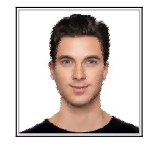
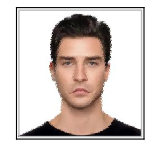
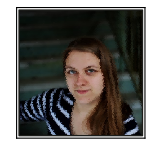
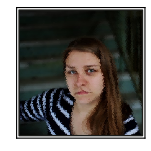
```mathematica
person1Happy = -Graphics-;person1Sad =-Graphics-;person2Happy = -Graphics-;person2Sad = -Graphics-;
```

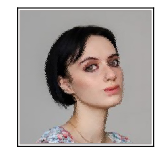
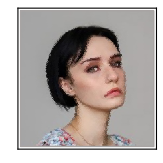
```mathematica
person3Happy=-Graphics-;person3Sad=-Graphics-;person4Happy=-Graphics-;person4Sad=-Graphics-;
```

```mathematica
daenerysHappy=-Graphics-;daenerysSad=-Graphics-;jonHappy=-Graphics-;jonSad=-Graphics-;
```

```mathematica
sansaHappy=-Graphics-;sansaSad=-Graphics-;khalHappy=-Graphics-;khalSad=-Graphics-;
```

### Side by side comparison with original photos for different expressions is as below. [Please uncomment respective code to see outputs for other faces.This is done to keep size of notebook low.]

```mathematica
GraphicsRow[{person1,person1Happy,person1Sad},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{person2,person2Happy,person2Sad},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{person3,person3Happy,person3Sad},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{person4,person4Happy,person4Sad},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{daenerys,daenerysHappy,daenerysSad},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{jon,jonHappy,jonSad},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{khal,khalHappy,khalSad},ImageSize->Large]*)
```

```mathematica
GraphicsRow[{sansa,sansaHappy,sansaSad},ImageSize->Large]
```

-Graphics-

### Chernoff Photos #2

In the second part of the project, you are asked to do something interesting with your Chernoff photo-faces method from Part #1. What do I mean by “interesting”? Below are some suggestions, but please feel free to think up your own. Creativity will be rewarded.

Example #1: Mathematica’s function CurrentImage[] gets an image from the computer’s camera. Use the CurrentImage[] as input to the Chernoff photo-face by making the eyes look in whatever direction things are changing the most.

Example #2: Choose a .wav file of a poem and have the Chernoff photo-face “read” the poem with expressions.

Example #3: Choose a .wav file of a song and have the Chernoff photo - face "dance" in response to the music.

Example #4: Pick a data set and have the Chernoff photo-face move in response to the data. The data may be from anywhere: NASA has lots of data from sunspots, think of animating weather-pattern data. There is a large variety of “curated data” available right from within Mathematica:

```mathematica
URL["https://reference.wolfram.com/language/howto/UseCuratedData.html"]
```

URL[https://reference.wolfram.com/language/howto/UseCuratedData.html]

These include AstronomicalData, ChemicalData, CityData, CountryData, ExampleData, ElementData, FinancialData, GraphData, IsotopeData, KnotData, LatticeData, ParticleData, PolyhedronData, WordData. Of course you can pick other data as you wish.

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### 1. Chernoff face variations for temperature data

```mathematica
chernoffFaceAnimateWithWeatherData[image_]:=Module[{},
(* This method takes temperature data for Chicago and creates an animation using the input image which shows different expression based on temperature*)

(*Function to change eye features in a face*)
(*This function enlarges/diminishes eye by calculating the mean position of all eye points 
and then using the slope of each eye point from the mean position to get the direction in which to
enlarge/diminish the eye. Here the diff variable captures the slope(direction of change for x and y coordinates).*)
manipulateEyes[grid_,leftEyeIndex_,rightEyeIndex_,scale_]:=Module[{},tempGrid=grid;
leftEyeCenter=Mean[tempGrid[[leftEyeIndex]]];
For[i=1,i≤Length[leftEyeIndex],i++,diff=tempGrid[[leftEyeIndex[[i]]]]-leftEyeCenter;
tempGrid[[leftEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[leftEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

rightEyeCenter=Mean[tempGrid[[rightEyeIndex]]];
For[i=1,i≤Length[rightEyeIndex],i++,diff=tempGrid[[rightEyeIndex[[i]]]]-rightEyeCenter;
tempGrid[[rightEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[rightEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

tempGrid];

(*Function to change mouth features in a face*)
(*This function alters the smile points by first calculating the mean position of all mouth points
and then based on the square of the distance from the mean position, the y-coordinate of all
mouth positions are increased/decreased to create smile/frown.*)
manipulateMouth[grid_,mouthIndex_,scale_]:=Module[{},tempGrid=grid;
For[i=1,i≤Length[mouthIndex],i++,
tempGrid[[mouthIndex[[i]]]][[2]]+=scale*(tempGrid[[mouthIndex[[i]]]][[1]]-Mean[tempGrid[[mouthIndex]]][[1]])^2;];
tempGrid];

(*Function to change eyebrow features in a face*)
(*This function alters the eyebrow points by first calculating mean position for both left and right eyebrow points.
Then based on scale value, it increases/decreases the y coordinates of eyebrow points based on whether an
eyebrow point is left/right of the mean position for each eyebrow. Amount of change is relative to difference
between x-coordinates of mean eyebrow point and the eyebrow point. *)
manipulateEyeBrows[grid_,leftEyeBrowIndex_,rightEyeBrowIndex_,scale_]:=Module[{},tempGrid=grid;
temp=scale;
For[i=1,i≤Length[leftEyeBrowIndex],i++,If[i≤Length[leftEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[leftEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[leftEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[leftEyeBrowIndex]]][[1]]);];
temp=scale;
For[i=1,i≤Length[rightEyeBrowIndex],i++,If[i≤Length[rightEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[rightEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[rightEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[rightEyeBrowIndex]]][[1]]);];
tempGrid];

(*Create a grid of points for interpolating facial points and change facial expressions *)
gridSize=30;
grid=Flatten[Table[{i,j},{i,0,1,1/(gridSize-1)},{j,0,1,1/(gridSize-1)}],1];

(*Find normalized coordinates for both the left and right eyes features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyePoints=FacialFeatures[image,"LeftEyePoints"][[1]];
leftEyePoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyePoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyePoints=FacialFeatures[image,"RightEyePoints"][[1]];
rightEyePoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyePoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyePointsIndex=Nearest[grid->"Index",leftEyePoints];
nearestRightEyePointsIndex=Nearest[grid->"Index",rightEyePoints];

(*Find normalized coordinates for mouth features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
mouthPoints=FacialFeatures[image,"MouthExternalPoints"][[1]];
mouthPoints[[All,1]]/=ImageDimensions[image][[1]];
mouthPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestMouthPointsIndex=Nearest[grid->"Index",mouthPoints];

(*Find normalized coordinates for both the left and right eyebrow features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyeBrowPoints=FacialFeatures[image,"LeftEyebrowPoints"][[1]];
leftEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyeBrowPoints=FacialFeatures[image,"RightEyebrowPoints"][[1]];
rightEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyeBrowPointsIndex=Nearest[grid->"Index",leftEyeBrowPoints];
nearestRightEyeBrowPointsIndex=Nearest[grid->"Index",rightEyeBrowPoints];

(*We have picked the WeatherData Dataset, which gives the measurements of the specified weather property at the given location.
In this case, we have taken temperature for Chicago from 1 Jan, 2017 to 3 Jan, 2017 in Degree Celsius.
Here,we can see that chernoff Face is changing(becoming sad/neutral/happy) in response to the data.*)

dataVal=WeatherData["Chicago","Temperature",{{2017,1,1},{2017,1,3}}];

(*Deleting the Missing data points and removing the units of data*)
list=DeleteCases[dataVal[[2]][[1]][[1]],_Missing];
list=QuantityMagnitude[list];
OutputList={};

(*Tracking the Maximum and Minimum values in the data to adjust the values of the scale values to be given for face manipulation.*)
MaxvalList=Max[list];
MinvalList=Min[list];
RangeList=MaxvalList-MinvalList;

(*Iterating over the List of data,and sending the corresponding scaled values in manipulateMouth,manipulateEyeBrows and manipulateEyes respectively*)
For[k=1,k≤Length[list]/3,k++,colorFunction=BSplineFunction[ImageData[image],SplineDegree->1];
MouthRange=(((list[[k]]-MinvalList)/(RangeList)))*20-10;
intermediateGrid=manipulateMouth[grid,Flatten[nearestMouthPointsIndex],MouthRange];
EyeBrowRange=(((list[[k]]-MinvalList)/(RangeList)))* 0.6-0.3;
intermediateGrid=manipulateEyeBrows[intermediateGrid,Flatten[nearestLeftEyeBrowPointsIndex],Flatten[nearestRightEyeBrowPointsIndex],EyeBrowRange];
EyeRange=(((list[[k]]-MinvalList)/(RangeList)))*0.5-0.25;
intermediateGrid=manipulateEyes[intermediateGrid,Flatten[nearestLeftEyePointsIndex],Flatten[nearestRightEyePointsIndex],EyeRange];
f=Interpolation[Flatten[Table[{{N[1/(gridSize-1)] i,N[1/(gridSize-1)] j},intermediateGrid[[gridSize i+j+1]]},{i,0,gridSize-1},{j,0,gridSize-1}],1],Method->"Spline",InterpolationOrder->1];
x=ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colorFunction[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,200],Mesh->None,ImageSize->300,PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None,AspectRatio->ImageAspectRatio[image]];
AppendTo[OutputList,x];];
{OutputList,list[[1;;Length[list]/3]]}
]
```

```mathematica
SetAttributes[chernoffFaceAnimateWithWeatherData,HoldAll];
{animation1,valuesList1}=chernoffFaceAnimateWithWeatherData[person1];
Row[{ListAnimate[animation1,5],ListAnimate[valuesList1,5,FrameLabel->Temperature (Celsius)]}]
```

### We can see that the facial expression of the person is changing with variation in temperature data.

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### 2. Chernoff face variations for latitude data

```mathematica
chernoffFaceAnimateWithCountryLatitudeData[image_]:=Module[{},

(*Function to change eye features in a face*)
(*This function enlarges/diminishes eye by calculating the mean position of all eye points 
and then using the slope of each eye point from the mean position to get the direction in which to
enlarge/diminish the eye. Here the diff variable captures the slope(direction of change for x and y coordinates).*)
manipulateEyes[grid_,leftEyeIndex_,rightEyeIndex_,scale_]:=Module[{},tempGrid=grid;
leftEyeCenter=Mean[tempGrid[[leftEyeIndex]]];
For[i=1,i≤Length[leftEyeIndex],i++,diff=tempGrid[[leftEyeIndex[[i]]]]-leftEyeCenter;
tempGrid[[leftEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[leftEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

rightEyeCenter=Mean[tempGrid[[rightEyeIndex]]];
For[i=1,i≤Length[rightEyeIndex],i++,diff=tempGrid[[rightEyeIndex[[i]]]]-rightEyeCenter;
tempGrid[[rightEyeIndex[[i]]]][[1]]+=scale*diff[[1]];
tempGrid[[rightEyeIndex[[i]]]][[2]]+=scale*diff[[2]];];

tempGrid];

(*Function to change mouth features in a face*)
(*This function alters the smile points by first calculating the mean position of all mouth points
and then based on the square of the distance from the mean position, the y-coordinate of all
mouth positions are increased/decreased to create smile/frown.*)
manipulateMouth[grid_,mouthIndex_,scale_]:=Module[{},tempGrid=grid;
For[i=1,i≤Length[mouthIndex],i++,
tempGrid[[mouthIndex[[i]]]][[2]]+=scale*(tempGrid[[mouthIndex[[i]]]][[1]]-Mean[tempGrid[[mouthIndex]]][[1]])^2;];
tempGrid];

(*Function to change eyebrow features in a face*)
(*This function alters the eyebrow points by first calculating mean position for both left and right eyebrow points.
Then based on scale value, it increases/decreases the y coordinates of eyebrow points based on whether an
eyebrow point is left/right of the mean position for each eyebrow. Amount of change is relative to difference
between x-coordinates of mean eyebrow point and the eyebrow point. *)
manipulateEyeBrows[grid_,leftEyeBrowIndex_,rightEyeBrowIndex_,scale_]:=Module[{},tempGrid=grid;
temp=scale;
For[i=1,i≤Length[leftEyeBrowIndex],i++,If[i≤Length[leftEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[leftEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[leftEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[leftEyeBrowIndex]]][[1]]);];
temp=scale;
For[i=1,i≤Length[rightEyeBrowIndex],i++,If[i≤Length[rightEyeBrowIndex]/2,temp=scale,temp=-1 scale];
tempGrid[[rightEyeBrowIndex[[i]]]][[2]]+=temp*(tempGrid[[rightEyeBrowIndex[[i]]]][[1]]-Mean[tempGrid[[rightEyeBrowIndex]]][[1]]);];
tempGrid];

(*Create a grid of points for interpolating facial points and change facial expressions *)
gridSize=30;
grid=Flatten[Table[{i,j},{i,0,1,1/(gridSize-1)},{j,0,1,1/(gridSize-1)}],1];

(*Find normalized coordinates for both the left and right eyes features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyePoints=FacialFeatures[image,"LeftEyePoints"][[1]];
leftEyePoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyePoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyePoints=FacialFeatures[image,"RightEyePoints"][[1]];
rightEyePoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyePoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyePointsIndex=Nearest[grid->"Index",leftEyePoints];
nearestRightEyePointsIndex=Nearest[grid->"Index",rightEyePoints];

(*Find normalized coordinates for mouth features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
mouthPoints=FacialFeatures[image,"MouthExternalPoints"][[1]];
mouthPoints[[All,1]]/=ImageDimensions[image][[1]];
mouthPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestMouthPointsIndex=Nearest[grid->"Index",mouthPoints];

(*Find normalized coordinates for both the left and right eyebrow features in the image , 
and then find the corresponding nearest points in the interpolation grid created above*)
leftEyeBrowPoints=FacialFeatures[image,"LeftEyebrowPoints"][[1]];
leftEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
leftEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

rightEyeBrowPoints=FacialFeatures[image,"RightEyebrowPoints"][[1]];
rightEyeBrowPoints[[All,1]]/=ImageDimensions[image][[1]];
rightEyeBrowPoints[[All,2]]/=ImageDimensions[image][[2]];

nearestLeftEyeBrowPointsIndex=Nearest[grid->"Index",leftEyeBrowPoints];
nearestRightEyeBrowPointsIndex=Nearest[grid->"Index",rightEyeBrowPoints];

(*We have picked the Country Data,which gives the value of the specified property for the countries.
Here,we have used the latitude of the country location as our changing data.
The chernoff Face is changing(becoming sad/neutral/happy) in response to the variation in data.*)

dataVal=CountryData[#,"Coordinates"]&/@CountryData[];
list=DeleteCases[dataVal,_Missing];
list=list[[1]][[1]][[1;;249]][[All,1]];
list=QuantityMagnitude[list];
OutputList={};

(*Tracking the Maximum and Minimum values in the data to adjust the values of the scale values to be given for face manipulation.*)
MaxvalList=Max[list];
MinvalList=Min[list];
RangeList=MaxvalList-MinvalList;

(*Iterating over the List of data,and sending the corresponding scaled values in manipulateMouth,manipulateEyeBrows and manipulateEyes respectively*)
For[k=1,k≤Length[list]/3,k++,colorFunction=BSplineFunction[ImageData[image],SplineDegree->1];
MouthRange=(((list[[k]]-MinvalList)/(RangeList)))*20-10;
intermediateGrid=manipulateMouth[grid,Flatten[nearestMouthPointsIndex],MouthRange];
EyeBrowRange=(((list[[k]]-MinvalList)/(RangeList)))* 0.6-0.3;
intermediateGrid=manipulateEyeBrows[intermediateGrid,Flatten[nearestLeftEyeBrowPointsIndex],Flatten[nearestRightEyeBrowPointsIndex],EyeBrowRange];
EyeRange=(((list[[k]]-MinvalList)/(RangeList)))*0.5-0.25;
intermediateGrid=manipulateEyes[intermediateGrid,Flatten[nearestLeftEyePointsIndex],Flatten[nearestRightEyePointsIndex],EyeRange];
f=Interpolation[Flatten[Table[{{N[1/(gridSize-1)] i,N[1/(gridSize-1)] j},intermediateGrid[[gridSize i+j+1]]},{i,0,gridSize-1},{j,0,gridSize-1}],1],Method->"Spline",InterpolationOrder->1];
x=ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colorFunction[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,200],Mesh->None,ImageSize->300,PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None,AspectRatio->ImageAspectRatio[image]];
AppendTo[OutputList,x];];
{OutputList,list[[1;;Length[list]/3]]}
]
```

```mathematica
(*SetAttributes[chernoffFaceAnimateWithCountryLatitudeData,HoldAll];
{animation2,valuesList2}=chernoffFaceAnimateWithCountryLatitudeData[person1];
Row[{ListAnimate[animation2,15],ListAnimate[valuesList2,15,FrameLabel->latitude]}]*)
```

### We can see that the facial expression of the person is changing with variation in latitude data. [Please uncomment and evaluate above three lines to see the Chernoff face variations for latitude data.]